```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Das folgende Programm gilt für homogene Differentialgleichungssysteme in der Form:

ⅆ/ⅆt 𝓎(t)=𝒜·𝓎(t)

Die Lösung eines allgemeinen Differentialgleichungssystems erhält man wie folgt:

𝓎(t)=ⅇ^(t·𝒜)·(𝓋_0+∫_0^t ⅇ^(-τ·𝒜)·𝓈(τ)ⅆτ)=ⅇ^(t·𝒜)·𝓋_0+∫_0^t ⅇ^((t-τ)·𝒜)·𝓈(τ)ⅆτ=Re[ⅇ^(t·𝒜)]·𝓋_0+∫_0^t Re[ⅇ^((t-τ)·𝒜)]·𝓈(τ)ⅆτ

Durch Diagonalisierung (Auflistung der Eigenvektoren in der Matrix 𝒫 und den Eigenwerten λ auf der Hauptdiagonalen der Diagonalmatrix 𝒟) des Matrixexponentials folgt:

𝓎(t)=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒫^-1]·𝓋_0+∫_0^t Re[𝒫·𝒟[ⅇ^(λ·(t-τ))]·𝒫^-1]·𝓈[τ]ⅆτ

Hinweis zum Programm: Realteilbildung von 𝓎(t) optional bereits in der allgemeinen Lösung möglich (ComplexExpand[Re[…]] um das Matrixexponential)

## Eingabe (𝒜, 𝓈(t))

```mathematica
ClearAll["Global`*"]
𝒜=({{0, 1, 0, 0}, {-2, -4, 0, 0}, {0, 0, 0, 1}, {0, 0, -9, -7}})//N;
𝓈[t_]=({{0}, {2}, {0}, {7}})//N;
```

## Eingabe (𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃)

Die Nebenbedingungen des Differentialgleichungssystems werden wie folgt defniniert:

```mathematica
𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃=({{Funktion, Zeit, Wert}});
```

```mathematica
𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃=({{1, 0, 0}, {2, 1, 1}, {3, 0, 1}, {4, 1, 2}})//N;
```

```mathematica
(*Ausgabe*)
Print[StringForm["Nebenbedingungen:\n``\n→ Es handelt sich um ein `` Differentialgleichungssystem.",
TableForm[Table[
{Subscript[y, Rationalize[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]},
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}],TableHeadings->{None,{"Funktion","Zeit","Wert"}}],
Which[
Length[𝒜]==Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"bestimmtes",
Length[𝒜]<Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"überbestimmtes",
Length[𝒜]>Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"unterbestimmtes"]]]
```

Nebenbedingungen:
Funktion | Zeit | Wert
y_1 | 0. | 0.
y_2 | 1. | 1.
y_3 | 0. | 1.
y_4 | 1. | 2.
→ Es handelt sich um ein bestimmtes Differentialgleichungssystem.

## Programm (allgemein)

```mathematica
(*Programm*)
𝓎1[t_]=Chop[MatrixExp[t 𝒜]];
𝓎2[t_]=Chop[Integrate[𝓎1[t-τ].𝓈[τ],{τ,0,t}]];
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t_]=Flatten[𝓎1[t].Table[{Subscript[v, i]},{i,Length[𝒜]}]+𝓎2[t]];

(*Ausgabe*)
Print[StringForm["𝓎_allgemein(t) = ``",
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]//MatrixForm]]
```

𝓎_allgemein(t) = …

## Programm (allgemein, diagonalisiert)

```mathematica
(*Programm*)
λ=Chop[Eigenvalues[𝒜]];
𝒫=Chop[Transpose[Eigenvectors[𝒜]]];
𝓎1[t_]=Chop[𝒫.DiagonalMatrix[Exp[λ t]].Inverse[𝒫]];
𝓎2[t_]=Chop[Integrate[𝓎1[t-τ].𝓈[τ],{τ,0,t}]];
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t_]=Flatten[𝓎1[t].Table[{Subscript[v, i]},{i,Length[𝒜]}]+𝓎2[t]];

(*Ausgabe*)
Print[StringForm["λ = ``\n𝒫 = ``\n𝓎_allgemein(t) = ``",
λ//MatrixForm,
𝒫//MatrixForm,
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]//MatrixForm]]
```

λ = (-5.30278
-3.41421
-1.69722
-0.585786)
𝒫 = (0 | -0.281085 | 0 | 0.862856
0 | 0.959683 | 0 | -0.505449
-0.185314 | 0 | 0.507636 | 0
0.982679 | 0 | -0.861572 | 0)
𝓎_allgemein(t) = …

## Programm (bestimmt)

```mathematica
(*Programm*)
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Table[
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]]==𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[v, i],{i,Length[𝒜]}]]][[2]];
𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=-Transpose[{Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[v, i],{i,Length[𝒜]}]]][[1]]}];
𝓋=Flatten[LinearSolve[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃]];

𝓇ℯℊℯℓ𝓃={(a_ Cos[c_]+b_ Sin[c_]):>√(a^2+b^2) Cos[c-Arg[a+I b]],
(Cos[c_]+b_ Sin[c_]):>√(1+b^2)Cos[c-Arg[1+I b]],
(a_ Cos[c_]+Sin[c_]):>√(a^2+1)Cos[c-Arg[a+I ]],
(Cos[c_]+Sin[c_]):>√2 Cos[c-π/4],
1.t:>t,-1.t:>-t,ⅇ^(1.t):>ⅇ^t,ⅇ^(-1.t):>ⅇ^-t};
𝓎[t_]=FullSimplify[Chop[ComplexExpand[Re[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]/.Table[Subscript[v, i]->𝓋[[i]],{i,Length[𝓋]}]]]]]/.𝓇ℯℊℯℓ𝓃;

(*Ausgabe*)
Print[StringForm["𝓋 = ``\n𝓎(t) = ``\n``",
𝓋//MatrixForm,
𝓎[t]//MatrixForm,
If[AllTrue[Table[Round[𝓎[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]],N[10^-9]]==Round[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],N[10^-9]],{i,Length[𝓋]}],TrueQ],
Style["→ Probe erfolgreich ☺",Darker[Green]],Style["→ Fehler aufgetreten ☹",Darker[Red]]]]]
```

𝓋 = (0.
-8.33155
1.
-26.5975)
𝓎(t) = (1.+3.15276 ⅇ^(-3.41421 t)-4.15276 ⅇ^(-0.585786 t)
-10.7642 ⅇ^(-3.41421 t)+2.43263 ⅇ^(-0.585786 t)
0.777778+7.2722 ⅇ^(-5.30278 t)-7.04998 ⅇ^(-1.69722 t)
-38.5629 ⅇ^(-5.30278 t)+11.9654 ⅇ^(-1.69722 t))
→ Probe erfolgreich ☺

## Programm (überbestimmt)

```mathematica
(*Programm*)
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Table[
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]]==𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[v, i],{i,Length[𝒜]}]]][[2]];
𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=-Transpose[{Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[v, i],{i,Length[𝒜]}]]][[1]]}];
𝓋=Flatten[LeastSquares[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃]];

𝓇ℯℊℯℓ𝓃={(a_ Cos[c_]+b_ Sin[c_]):>√(a^2+b^2) Cos[c-Arg[a+I b]],
(Cos[c_]+b_ Sin[c_]):>√(1+b^2)Cos[c-Arg[1+I b]],
(a_ Cos[c_]+Sin[c_]):>√(a^2+1)Cos[c-Arg[a+I ]],
(Cos[c_]+Sin[c_]):>√2 Cos[c-π/4],
1.t:>t,-1.t:>-t,ⅇ^(1.t):>ⅇ^t,ⅇ^(-1.t):>ⅇ^-t};
𝓎[t_]=FullSimplify[Chop[ComplexExpand[Re[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]/.Table[Subscript[v, i]->𝓋[[i]],{i,Length[𝓋]}]]]]]/.𝓇ℯℊℯℓ𝓃;

(*Ausgabe*)
Print[StringForm["𝓋 = ``\n𝓎(t) = ``",
𝓋//MatrixForm,
𝓎[t]//MatrixForm]]
```

𝓋 = (2.53596×10^-17
-8.33155
1.
-26.5975)
𝓎(t) = (1.+3.15276 ⅇ^(-3.41421 t)-4.15276 ⅇ^(-0.585786 t)
-10.7642 ⅇ^(-3.41421 t)+2.43263 ⅇ^(-0.585786 t)
0.777778+7.2722 ⅇ^(-5.30278 t)-7.04998 ⅇ^(-1.69722 t)
-38.5629 ⅇ^(-5.30278 t)+11.9654 ⅇ^(-1.69722 t))

## Programm (unterbestimmt)

```mathematica
(*Programm*)
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Table[
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]]==𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[v, i],{i,Length[𝒜]}]]][[2]];
𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=-Transpose[{Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[v, i],{i,Length[𝒜]}]]][[1]]}];
{𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃m,𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃n}=Dimensions[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃1=𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃[[All,1;;𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃m]];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃2=𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃[[All,𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃m+1;;𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃n]];
𝓇=Inverse[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃1].𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃;
𝒩=-Inverse[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃1].𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃2;
𝓋=Flatten[𝓇+𝒩.Table[{Subscript[v, i]},{i,𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃m+1,𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃n}]];

𝓇ℯℊℯℓ𝓃={(a_ Cos[c_]+b_ Sin[c_]):>√(a^2+b^2) Cos[c-Arg[a+I b]],
(Cos[c_]+b_ Sin[c_]):>√(1+b^2)Cos[c-Arg[1+I b]],
(a_ Cos[c_]+Sin[c_]):>√(a^2+1)Cos[c-Arg[a+I ]],
(Cos[c_]+Sin[c_]):>√2 Cos[c-π/4],
1.t:>t,-1.t:>-t,ⅇ^(1.t):>ⅇ^t,ⅇ^(-1.t):>ⅇ^-t};
𝓇ℯℊℯℓ𝓃𝒰𝓃𝓉ℯ𝓇𝒷ℯ𝓈𝓉𝒾𝓂𝓂𝓉={(a_ Cos[c_]+b_ Sin[c_])d_:>√(a^2+b^2) Cos[c-Arg[a+I b]]d,
(Cos[c_]+b_ Sin[c_])d_:>√(1+b^2)Cos[c-Arg[1+I b]]d,
(a_ Cos[c_]+Sin[c_])d_:>√(a^2+1)Cos[c-Arg[a+I ]]d,
(Cos[c_]+Sin[c_])d_:>√2 Cos[c-π/4]d};
𝓎[t_]=FullSimplify[Chop[ComplexExpand[Re[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]/.Table[Subscript[v, i]->𝓋[[i]],{i,Length[𝓋]}]]]]]/.𝓇ℯℊℯℓ𝓃/.𝓇ℯℊℯℓ𝓃𝒰𝓃𝓉ℯ𝓇𝒷ℯ𝓈𝓉𝒾𝓂𝓂𝓉;

(*Ausgabe*)
Print[StringForm["𝓋 = ``\n𝓎(t) = ``",
𝓋//MatrixForm,
𝓎[t]//MatrixForm]]
```

𝓋 = (0.
-8.33155
1.
-26.5975)
𝓎(t) = (1.+3.15276 ⅇ^(-3.41421 t)-4.15276 ⅇ^(-0.585786 t)
-10.7642 ⅇ^(-3.41421 t)+2.43263 ⅇ^(-0.585786 t)
0.777778+7.2722 ⅇ^(-5.30278 t)-7.04998 ⅇ^(-1.69722 t)
-38.5629 ⅇ^(-5.30278 t)+11.9654 ⅇ^(-1.69722 t))

## Plot

Unterbestimmter Fall: Bei dem Plot von 𝓎(t) müssen den übrigen Parametern v_i konstante Werte zugeordnet werden:

```mathematica
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,5};
𝓋𝒫ℓℴ𝓉={};
```

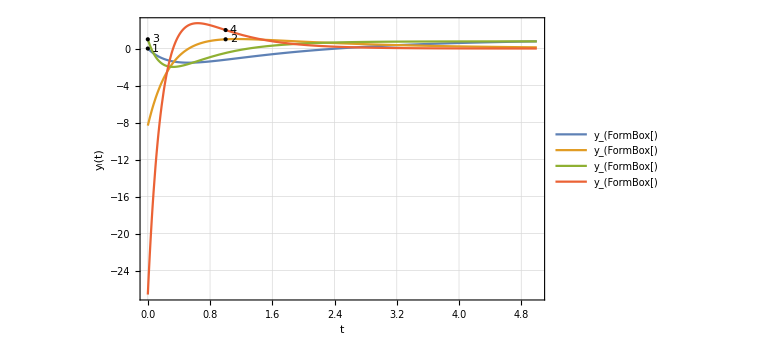

```mathematica
(*Ausgabe*)
plot=Plot[
Evaluate[𝓎[t]/.𝓋𝒫ℓℴ𝓉],{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
PlotRange->All,Frame->True,FrameLabel->{"t","y_i(t)"},GridLines->Automatic,
PlotLegends->Table[StringForm["y_(``)",i],{i,Length[𝓎[t]]}],
Epilog->
{Table[
Point[{𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]}],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}],
Table[
Text[i,{𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]+.1,𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]}],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}]},
ImageSize->Large];
Print[Show[plot]]
```

```mathematica
(*Ausgabe*)
Print[StringForm["y(5) = ``\ng(5) = ``",
𝓎[5][[1]],
𝓎[5][[3]]]]
```

y(5) = 0.778018
g(5) = 0.776323